^3

```mathematica
$PrePrint = If[MatrixQ[#], MatrixForm[#], #] &;
Clear[x]
Clear[t]
CW = {{0,0,0,1,0,0}, {0,0,0,0,1,0}, {0,0,0,0,0,1}, {3 * (x^2), 0, 0,0, 2*x, 0 }, {0,0,0, -2*x, 0,0}, {0, 0, -x^2, 0, 0,0}}
STM = FullSimplify[MatrixExp[CW * t].IdentityMatrix[6]]
STMRV = STM[[1 ;; 3, 4 ;; 6]]
decomp = SingularValueDecomposition[STMRV /. {t -> 1, x-> 1}];

(* STMRV /. {t } *)
```

(0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1
3 x^2 | 0 | 0 | 0 | 2 x | 0
0 | 0 | 0 | -2 x | 0 | 0
0 | 0 | -x^2 | 0 | 0 | 0)

(4-3 Cos[t x] | 0 | 0 | Sin[t x]/x | (2-2 Cos[t x])/x | 0
6 (-t x+Sin[t x]) | 1 | 0 | (2 (-1+Cos[t x]))/x | -3 t+(4 Sin[t x])/x | 0
0 | 0 | Cos[t x] | 0 | 0 | Sin[t x]/x
3 x Sin[t x] | 0 | 0 | Cos[t x] | 2 Sin[t x] | 0
6 x (-1+Cos[t x]) | 0 | 0 | -2 Sin[t x] | -3+4 Cos[t x] | 0
0 | 0 | -x Sin[t x] | 0 | 0 | Cos[t x])

(Sin[t x]/x | (2-2 Cos[t x])/x | 0
(2 (-1+Cos[t x]))/x | -3 t+(4 Sin[t x])/x | 0
0 | 0 | Sin[t x]/x)

```mathematica
transf = Transpose[{decomp[[1]][[All, 1]] * decomp[[2]][[1,1]],decomp[[1]][[All, 2]] * decomp[[2]][[2,2]],decomp[[1]][[All, 3]] * decomp[[2]][[3,3]] }]
func[u_, v_] = transf.{Cos[u]*Sin[v], Sin[u]*Sin[v], Cos[v]}
```

(1/2 (2-2 Cos[1]-(Sin[1] (-7+16 Cos[1]^2+9 Cos[2]-48 Sin[1]+64 Sin[1]^2-√((-59+32 Cos[1]+9 Cos[2]+48 Sin[1])^2-8 (201-256 Cos[1]+55 Cos[2]-96 Sin[1]+48 Sin[2]))))/(24 (-1+Cos[1]) (-1+Sin[1]))) √((59-32 Cos[1]-9 Cos[2]-48 Sin[1]+√((-59+32 Cos[1]+9 Cos[2]+48 Sin[1])^2-8 (201-256 Cos[1]+55 Cos[2]-96 Sin[1]+48 Sin[2])))/((3-4 Sin[1]+(-7+16 Cos[1]^2+9 Cos[2]-48 Sin[1]+64 Sin[1]^2-√((-59+32 Cos[1]+9 Cos[2]+48 Sin[1])^2-8 (201-256 Cos[1]+55 Cos[2]-96 Sin[1]+48 Sin[2])))/(12 (-1+Sin[1])))^2+(2-2 Cos[1]-(Sin[1] (-7+16 Cos[1]^2+9 Cos[2]-48 Sin[1]+64 Sin[1]^2-√((-59+32 Cos[1]+9 Cos[2]+48 Sin[1])^2-8 (201-256 Cos[1]+55 Cos[2]-96 Sin[1]+48 Sin[2]))))/(24 (-1+Cos[1]) (-1+Sin[1])))^2)) | 1/2 (2-2 Cos[1]-(Sin[1] (-7+16 Cos[1]^2+9 Cos[2]-48 Sin[1]+64 Sin[1]^2+√((-59+32 Cos[1]+9 Cos[2]+48 Sin[1])^2-8 (201-256 Cos[1]+55 Cos[2]-96 Sin[1]+48 Sin[2]))))/(24 (-1+Cos[1]) (-1+Sin[1]))) √((59-32 Cos[1]-9 Cos[2]-48 Sin[1]-√((-59+32 Cos[1]+9 Cos[2]+48 Sin[1])^2-8 (201-256 Cos[1]+55 Cos[2]-96 Sin[1]+48 Sin[2])))/((-3+4 Sin[1]-(-7+16 Cos[1]^2+9 Cos[2]-48 Sin[1]+64 Sin[1]^2+√((-59+32 Cos[1]+9 Cos[2]+48 Sin[1])^2-8 (201-256 Cos[1]+55 Cos[2]-96 Sin[1]+48 Sin[2])))/(12 (-1+Sin[1])))^2+(2-2 Cos[1]-(Sin[1] (-7+16 Cos[1]^2+9 Cos[2]-48 Sin[1]+64 Sin[1]^2+√((-59+32 Cos[1]+9 Cos[2]+48 Sin[1])^2-8 (201-256 Cos[1]+55 Cos[2]-96 Sin[1]+48 Sin[2]))))/(24 (-1+Cos[1]) (-1+Sin[1])))^2)) | 0
1/2 (-3+4 Sin[1]-(-7+16 Cos[1]^2+9 Cos[2]-48 Sin[1]+64 Sin[1]^2-√((-59+32 Cos[1]+9 Cos[2]+48 Sin[1])^2-8 (201-256 Cos[1]+55 Cos[2]-96 Sin[1]+48 Sin[2])))/(12 (-1+Sin[1]))) √((59-32 Cos[1]-9 Cos[2]-48 Sin[1]+√((-59+32 Cos[1]+9 Cos[2]+48 Sin[1])^2-8 (201-256 Cos[1]+55 Cos[2]-96 Sin[1]+48 Sin[2])))/((3-4 Sin[1]+(-7+16 Cos[1]^2+9 Cos[2]-48 Sin[1]+64 Sin[1]^2-√((-59+32 Cos[1]+9 Cos[2]+48 Sin[1])^2-8 (201-256 Cos[1]+55 Cos[2]-96 Sin[1]+48 Sin[2])))/(12 (-1+Sin[1])))^2+(2-2 Cos[1]-(Sin[1] (-7+16 Cos[1]^2+9 Cos[2]-48 Sin[1]+64 Sin[1]^2-√((-59+32 Cos[1]+9 Cos[2]+48 Sin[1])^2-8 (201-256 Cos[1]+55 Cos[2]-96 Sin[1]+48 Sin[2]))))/(24 (-1+Cos[1]) (-1+Sin[1])))^2)) | 1/2 (-3+4 Sin[1]-(-7+16 Cos[1]^2+9 Cos[2]-48 Sin[1]+64 Sin[1]^2+√((-59+32 Cos[1]+9 Cos[2]+48 Sin[1])^2-8 (201-256 Cos[1]+55 Cos[2]-96 Sin[1]+48 Sin[2])))/(12 (-1+Sin[1]))) √((59-32 Cos[1]-9 Cos[2]-48 Sin[1]-√((-59+32 Cos[1]+9 Cos[2]+48 Sin[1])^2-8 (201-256 Cos[1]+55 Cos[2]-96 Sin[1]+48 Sin[2])))/((-3+4 Sin[1]-(-7+16 Cos[1]^2+9 Cos[2]-48 Sin[1]+64 Sin[1]^2+√((-59+32 Cos[1]+9 Cos[2]+48 Sin[1])^2-8 (201-256 Cos[1]+55 Cos[2]-96 Sin[1]+48 Sin[2])))/(12 (-1+Sin[1])))^2+(2-2 Cos[1]-(Sin[1] (-7+16 Cos[1]^2+9 Cos[2]-48 Sin[1]+64 Sin[1]^2+√((-59+32 Cos[1]+9 Cos[2]+48 Sin[1])^2-8 (201-256 Cos[1]+55 Cos[2]-96 Sin[1]+48 Sin[2]))))/(24 (-1+Cos[1]) (-1+Sin[1])))^2)) | 0
0 | 0 | Sin[1])

{1/2 Cos[u] (2-2 Cos[1]-(Sin[1] (-7+16 Cos[1]^2+9 Cos[2]-48 Sin[1]+64 Sin[1]^2-√((-59+32 Cos[1]+9 Cos[2]+48 Sin[1])^2-8 (201-256 Cos[1]+55 Cos[2]-96 Sin[1]+48 Sin[2]))))/(24 (-1+Cos[1]) (-1+Sin[1]))) √((59-32 Cos[1]-9 Cos[2]-48 Sin[1]+√((-59+32 Cos[1]+9 Cos[2]+48 Sin[1])^2-8 (201-256 Cos[1]+55 Cos[2]-96 Sin[1]+48 Sin[2])))/((3-4 Sin[1]+(-7+16 Cos[1]^2+9 Cos[2]-48 Sin[1]+64 Sin[1]^2-√((-59+32 Cos[1]+9 Cos[2]+48 Sin[1])^2-8 (201-256 Cos[1]+55 Cos[2]-96 Sin[1]+48 Sin[2])))/(12 (-1+Sin[1])))^2+(2-2 Cos[1]-(Sin[1] (-7+16 Cos[1]^2+9 Cos[2]-48 Sin[1]+64 Sin[1]^2-√((-59+32 Cos[1]+9 Cos[2]+48 Sin[1])^2-8 (201-256 Cos[1]+55 Cos[2]-96 Sin[1]+48 Sin[2]))))/(24 (-1+Cos[1]) (-1+Sin[1])))^2)) Sin[v]+1/2 (2-2 Cos[1]-(Sin[1] (-7+16 Cos[1]^2+9 Cos[2]-48 Sin[1]+64 Sin[1]^2+√((-59+32 Cos[1]+9 Cos[2]+48 Sin[1])^2-8 (201-256 Cos[1]+55 Cos[2]-96 Sin[1]+48 Sin[2]))))/(24 (-1+Cos[1]) (-1+Sin[1]))) √((59-32 Cos[1]-9 Cos[2]-48 Sin[1]-√((-59+32 Cos[1]+9 Cos[2]+48 Sin[1])^2-8 (201-256 Cos[1]+55 Cos[2]-96 Sin[1]+48 Sin[2])))/((-3+4 Sin[1]-(-7+16 Cos[1]^2+9 Cos[2]-48 Sin[1]+64 Sin[1]^2+√((-59+32 Cos[1]+9 Cos[2]+48 Sin[1])^2-8 (201-256 Cos[1]+55 Cos[2]-96 Sin[1]+48 Sin[2])))/(12 (-1+Sin[1])))^2+(2-2 Cos[1]-(Sin[1] (-7+16 Cos[1]^2+9 Cos[2]-48 Sin[1]+64 Sin[1]^2+√((-59+32 Cos[1]+9 Cos[2]+48 Sin[1])^2-8 (201-256 Cos[1]+55 Cos[2]-96 Sin[1]+48 Sin[2]))))/(24 (-1+Cos[1]) (-1+Sin[1])))^2)) Sin[u] Sin[v],1/2 Cos[u] (-3+4 Sin[1]-(-7+16 Cos[1]^2+9 Cos[2]-48 Sin[1]+64 Sin[1]^2-√((-59+32 Cos[1]+9 Cos[2]+48 Sin[1])^2-8 (201-256 Cos[1]+55 Cos[2]-96 Sin[1]+48 Sin[2])))/(12 (-1+Sin[1]))) √((59-32 Cos[1]-9 Cos[2]-48 Sin[1]+√((-59+32 Cos[1]+9 Cos[2]+48 Sin[1])^2-8 (201-256 Cos[1]+55 Cos[2]-96 Sin[1]+48 Sin[2])))/((3-4 Sin[1]+(-7+16 Cos[1]^2+9 Cos[2]-48 Sin[1]+64 Sin[1]^2-√((-59+32 Cos[1]+9 Cos[2]+48 Sin[1])^2-8 (201-256 Cos[1]+55 Cos[2]-96 Sin[1]+48 Sin[2])))/(12 (-1+Sin[1])))^2+(2-2 Cos[1]-(Sin[1] (-7+16 Cos[1]^2+9 Cos[2]-48 Sin[1]+64 Sin[1]^2-√((-59+32 Cos[1]+9 Cos[2]+48 Sin[1])^2-8 (201-256 Cos[1]+55 Cos[2]-96 Sin[1]+48 Sin[2]))))/(24 (-1+Cos[1]) (-1+Sin[1])))^2)) Sin[v]+1/2 (-3+4 Sin[1]-(-7+16 Cos[1]^2+9 Cos[2]-48 Sin[1]+64 Sin[1]^2+√((-59+32 Cos[1]+9 Cos[2]+48 Sin[1])^2-8 (201-256 Cos[1]+55 Cos[2]-96 Sin[1]+48 Sin[2])))/(12 (-1+Sin[1]))) √((59-32 Cos[1]-9 Cos[2]-48 Sin[1]-√((-59+32 Cos[1]+9 Cos[2]+48 Sin[1])^2-8 (201-256 Cos[1]+55 Cos[2]-96 Sin[1]+48 Sin[2])))/((-3+4 Sin[1]-(-7+16 Cos[1]^2+9 Cos[2]-48 Sin[1]+64 Sin[1]^2+√((-59+32 Cos[1]+9 Cos[2]+48 Sin[1])^2-8 (201-256 Cos[1]+55 Cos[2]-96 Sin[1]+48 Sin[2])))/(12 (-1+Sin[1])))^2+(2-2 Cos[1]-(Sin[1] (-7+16 Cos[1]^2+9 Cos[2]-48 Sin[1]+64 Sin[1]^2+√((-59+32 Cos[1]+9 Cos[2]+48 Sin[1])^2-8 (201-256 Cos[1]+55 Cos[2]-96 Sin[1]+48 Sin[2]))))/(24 (-1+Cos[1]) (-1+Sin[1])))^2)) Sin[u] Sin[v],Cos[v] Sin[1]}

```mathematica
ParametricPlot3D[func[u, v],      {u, 0, 2 * Pi}, {v, 0, Pi}]
STMRV2d = [[1 ;;2, 4 ;; 5]]
decomp2d = SingularValueDecomposition[STMRV2d /. {t -> 10, x-> 1}];
transf2d = Transpose[{decomp2d[[1]][[All, 1]] * decomp2d[[2]][[1,1]],decomp2d[[1]][[All, 2]] * decomp2d[[2]][[2,2]] }]

func2d[theta_] = transf2d.{Cos[theta], Sin[theta]}
ParametricPlot[func2d[theta], {theta, 0, 2 * Pi}]
```

-Graphics3D-

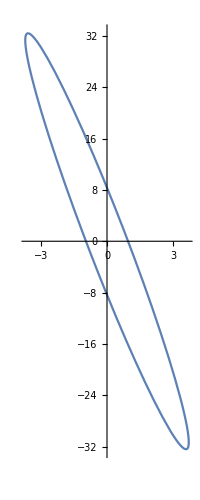

-Graphics3D-

-Graphics-

```mathematica
ParametricPlot [(STMRV[[1 ;; 2, 1 ;; 2]] /. {t ->10, x-> 1}).{Cos[theta], Sin[theta]}, {theta, 0, 2 * Pi}]
ParametricPlot3D [(STMRV /. {t ->1, x-> 1}).{Cos[u]*Sin[v], Sin[u]*Sin[v], Cos[v]}, {u, 0, 2 * Pi}, {v, 0, Pi}]
ImpulsivePlot = ParametricPlot [(STMRV[[1 ;; 2, 1 ;; 2]] /. {t ->10, x-> 1}).{Cos[theta], Sin[theta]}, {theta, 0, 2 * Pi}]
```

```mathematica
Manipulate[ParametricPlot [(STMRV[[1 ;; 2, 1 ;; 2]] /. {t ->t1, x-> 1}).{Cos[theta], Sin[theta]}, {theta, 0, 2 * Pi}], {t1, 0, 10}]
```

(3 t-(4 Sin[t x])/x | -(2 (1-Cos[t x]))/x | 0
-(2 (-1+Cos[t x]))/x | -Sin[t x]/x | 0
-(3 t^2)/2+(4 (1-Cos[t x]))/x^2 | (2 (t x-Sin[t x]))/x^2 | 0
(2 (-t x+Sin[t x]))/x^2 | (1-Cos[t x])/x^2 | 0
-(1-Cos[t x])/x^2 | 0 | 0
-Sin[t x]/x | 0 | 0)

((1-Cos[t x])/x^2 | -(2 (-t x+Sin[t x]))/x^2 | 0
(2 (-t x+Sin[t x]))/x^2 | -(3 t^2)/2+(4 (1-Cos[t x]))/x^2 | 0
0 | 0 | (1-Cos[t x])/x^2
Sin[t x]/x | (2 (-1+Cos[t x]))/x | 0
(2 (-1+Cos[t x]))/x | -3 t+(4 Sin[t x])/x | 0
0 | 0 | Sin[t x]/x)

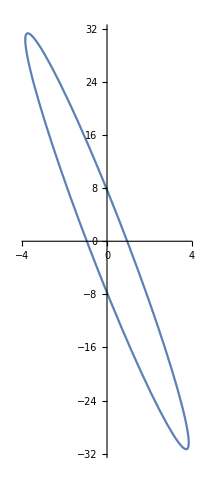

-Graphics-

```mathematica
$PrePrint = If[MatrixQ[#], MatrixForm[#], #] &;
ITM = {{(-4 / x) * Sin[x * t] + 3 * t, -((2/x) * (1 - Cos[x * t])), 0}, {-(2 / x) *( Cos[x * t] - 1), -(1/x)* Sin[x * t], 0}, {(4/x^2) * (1 - Cos[x * t]) - (3 * t^2) / 2, (2 / x^2 ) * (x * t - Sin[x * t]), 0},{(2/x^2) * (Sin[x*t] - x*t), (1/x^2)*(1 - Cos[x*t]), 0}, {(-1/x^2) * (1 - Cos[x * t]), 0,0 }, {(-1/x) * Sin[x*t], 0, 0}}


itm={{(1-Cos[t x])/x^2,(-2 (-t x+Sin[t x]))/x^2,0},{(2 (-t x+Sin[t x]))/x^2,-(3 t^2)/2+(4 (1-Cos[t x]))/x^2,0},{0,0,(1-Cos[t x])/x^2},{Sin[t x]/x,(2 (-1+Cos[t x]))/x,0},{(2 (-1+Cos[t x]))/x,-3 t+(4 Sin[t x])/x,0},{0,0,Sin[t x]/x}}
STM;
STM[[1 ;; 3, 1 ;; 6]];
decomp2d = SingularValueDecomposition[((STM[[1 ;; 3, 1 ;; 6]] /. {t -> 9.9, x-> 1}).(itm /. { t-> 0.1 ,x-> 1} ))[[1;;2,1;;2]] / 0.1];
transf2d = Transpose[{decomp2d[[1]][[All, 1]] * decomp2d[[2]][[1,1]],decomp2d[[1]][[All, 2]] * decomp2d[[2]][[2,2]] }];
func2d[theta_] = transf2d.{Cos[theta], Sin[theta]};
ParametricPlot[func2d[theta], {theta, 0, 2 * Pi}]
```

```mathematica
({{3 t-(4 Sin[t x])/x, -(2 (1-Cos[t x]))/x, 0}, {-(2 (-1+Cos[t x]))/x, -Sin[t x]/x, 0}, {-(3 t^2)/2+(4 (1-Cos[t x]))/x^2, (2 (t x-Sin[t x]))/x^2, 0}, {(2 (-t x+Sin[t x]))/x^2, (1-Cos[t x])/x^2, 0}, {-(1-Cos[t x])/x^2, 0, 0}, {-Sin[t x]/x, 0, 0}})
```

(3 t-(4 Sin[t x])/x | -(2 (1-Cos[t x]))/x | 0
-(2 (-1+Cos[t x]))/x | -Sin[t x]/x | 0
-(3 t^2)/2+(4 (1-Cos[t x]))/x^2 | (2 (t x-Sin[t x]))/x^2 | 0
(2 (-t x+Sin[t x]))/x^2 | (1-Cos[t x])/x^2 | 0
-(1-Cos[t x])/x^2 | 0 | 0
-Sin[t x]/x | 0 | 0)

```mathematica
itm={{(1-Cos[t x])/x^2,(-2 (-t x+Sin[t x]))/x^2,0},{(2 (-t x+Sin[t x]))/x^2,-(3 t^2)/2+(4 (1-Cos[t x]))/x^2,0},{0,0,(1-Cos[t x])/x^2},{Sin[t x]/x,(2 (-1+Cos[t x]))/x,0},{(2 (-1+Cos[t x]))/x,-3 t+(4 Sin[t x])/x,0},{0,0,Sin[t x]/x}}
```

((1-Cos[t x])/x^2 | -(2 (-t x+Sin[t x]))/x^2 | 0
(2 (-t x+Sin[t x]))/x^2 | -(3 t^2)/2+(4 (1-Cos[t x]))/x^2 | 0
0 | 0 | (1-Cos[t x])/x^2
Sin[t x]/x | (2 (-1+Cos[t x]))/x | 0
(2 (-1+Cos[t x]))/x | -3 t+(4 Sin[t x])/x | 0
0 | 0 | Sin[t x]/x)

```mathematica
(*X=y
Y=-z
Z=-x*)
```

```mathematica
MatrixForm[itm]
```

^2 ((1-Cos[t x])/x^2 | -(2 (-t x+Sin[t x]))/x^2 | 0
(2 (-t x+Sin[t x]))/x^2 | -(3 t^2)/2+(4 (1-Cos[t x]))/x^2 | 0
0 | 0 | (1-Cos[t x])/x^2
Sin[t x]/x | (2 (-1+Cos[t x]))/x | 0
(2 (-1+Cos[t x]))/x | -3 t+(4 Sin[t x])/x | 0
0 | 0 | Sin[t x]/x)

```mathematica
MatrixForm[Normal[Series[itm/.{x->1},{t,0,2}]]]

Eigensystem[{(STM[[1 ;; 3, 1 ;; 6]] /. {t -> 9.9, x-> 1}) .(itm /. { t-> 0.1 ,x-> 1})  [[1;;2,1;;2]], STM[[1 ;;2, 4 ;; 5]]/. {t -> 1, x-> 1}}]
```

(t^2/2 | 0 | 0
0 | t^2/2 | 0
0 | 0 | t^2/2
t | -t^2 | 0
-t^2 | t | 0
0 | 0 | t)

Dot::dotsh: Tensors {{6.66757,0,0,-0.457536,3.77838,0},{-62.1452,1,0,-3.77838,-31.5301,0},{0,0,-0.889191,0,0,-0.457536}} and {{0.00499583,0.000333167},{-0.000333167,0.00498334}} have incompatible shapes.

Eigensystem[{{{6.66757,0,0,-0.457536,3.77838,0},{-62.1452,1,0,-3.77838,-31.5301,0},{0,0,-0.889191,0,0,-0.457536}}.{{0.00499583,0.000333167},{-0.000333167,0.00498334}},{{Sin[1],2-2 Cos[1]},{2 (-1+Cos[1]),-3+4 Sin[1]}}}]

```mathematica
PlotReachableSetConst[n_, t1_, t2_]:=Module[{decomp2d, transf2d},decomp2d = SingularValueDecomposition[((STM[[1 ;; 3, 1 ;; 6]] /. {t -> t2, x-> n}).(itm /. { t-> t1 ,x-> n} ))[[1;;2,1;;2]] / t1];
ParametricPlot[ Transpose[{decomp2d[[1]][[All, 1]] * decomp2d[[2]][[1,1]],decomp2d[[1]][[All, 2]] * decomp2d[[2]][[2,2]] }].{Cos[theta], Sin[theta]}, {theta, 0, 2 * Pi}]
]

PlotReachableSetConst[1, 0.1, 9.9]
Manipulate[PlotReachableSetConst[1, t1, 10 - t1],{t1, 0.001, 3}]
```

-Graphics-

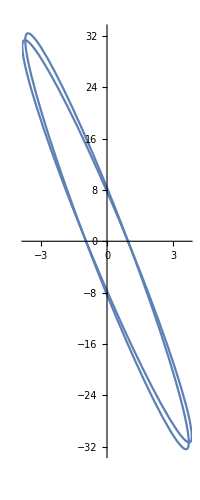

```mathematica
Show[ImpulsivePlot, PlotReachableSetConst[1, 0.1, 9.9]]
```

```mathematica
(STM[[1 ;; 3, 1 ;; 6]] /. {t -> (10 - t_1), x-> 1}) .(itm /. { t-> t_1 ,x-> 1})
```

((4-3 Cos[10-t_]) (1-Cos[t_])+2 (2-2 Cos[10-t_]) (-1+Cos[t_])+Sin[10-t_] Sin[t_] | 2 (-1+Cos[t_]) Sin[10-t_]-2 (4-3 Cos[10-t_]) (-t_+Sin[t_])+(2-2 Cos[10-t_]) (-3 t_+4 Sin[t_]) | 0
6 (1-Cos[t_]) (-10+t_+Sin[10-t_])+2 (-1+Cos[t_]) (-3 (10-t_)+4 Sin[10-t_])+2 (-1+Cos[10-t_]) Sin[t_]+2 (-t_+Sin[t_]) | 4 (1-Cos[t_])+4 (-1+Cos[10-t_]) (-1+Cos[t_])-(3 t_^2)/2-12 (-10+t_+Sin[10-t_]) (-t_+Sin[t_])+(-3 (10-t_)+4 Sin[10-t_]) (-3 t_+4 Sin[t_]) | 0
0 | 0 | Cos[10-t_] (1-Cos[t_])+Sin[10-t_] Sin[t_])

```mathematica
Det[((STM[[1 ;; 3, 1 ;; 6]] /. {t -> (t2 - t1), x-> 1}) .(itm /. { t-> t1 ,x-> 1}))  [[1;;2,1;;2]]]
```

4 t1^2+8 Cos[t1-t2]+3/2 t1^2 Cos[t1-t2]-3 t1 t2 Cos[t1-t2]-16 Cos[t1] Cos[t1-t2]-3/2 t1^2 Cos[t1] Cos[t1-t2]+3 t1 t2 Cos[t1] Cos[t1-t2]+8 Cos[t1]^2 Cos[t1-t2]-4 Cos[t1-t2]^2+8 Cos[t1] Cos[t1-t2]^2-4 Cos[t1]^2 Cos[t1-t2]^2-8 t1 Cos[t1-t2] Sin[t1]+4 Cos[t1-t2]^2 Sin[t1]^2-8 Sin[t1] Sin[t1-t2]-3/2 t1^2 Sin[t1] Sin[t1-t2]+3 t1 t2 Sin[t1] Sin[t1-t2]+8 Cos[t1] Sin[t1] Sin[t1-t2]-4 Sin[t1-t2]^2+8 Cos[t1] Sin[t1-t2]^2-4 Cos[t1]^2 Sin[t1-t2]^2+4 Sin[t1]^2 Sin[t1-t2]^2

```mathematica
NSolve[Det[((STM[[1 ;; 3, 1 ;; 6]] /. {t -> ( - t1), x-> 1}) .(itm /. { t-> t1 ,x-> 1}))  [[1;;2,1;;2]]] == 0, t1]
```

NSolve::nsmet: This system cannot be solved with the methods available to NSolve.

NSolve[4 t1^2+8 Cos[t1]+3/2 t1^2 Cos[t1]-20 Cos[t1]^2-3/2 t1^2 Cos[t1]^2+16 Cos[t1]^3-4 Cos[t1]^4-8 t1 Cos[t1] Sin[t1]-12 Sin[t1]^2-3/2 t1^2 Sin[t1]^2+16 Cos[t1] Sin[t1]^2+4 Sin[t1]^4==0,t1]

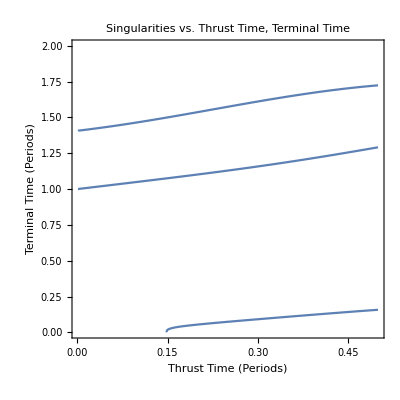

/Users/maxzweig/energythrust

singularities/singularitiesn1.png

```mathematica
plot = ContourPlot[Det[((STM[[1 ;; 3, 1 ;; 6]] /. {t -> (t2 2 Pi - t1 2 Pi), x-> 1}) .(itm /. { t-> t1 2 Pi ,x-> 1}))  [[1;;2,1;;2]]]==0, {t1, 0.001, 1/2}, {t2, 0.001, 2}, (** PlotLabel-> "Singularities vs. Thrust Time, Terminal Time", **) FrameLabel->{"Thrust Time (Periods)", "Terminal Time (Periods)"}, PlotPoints-> 20, MaxRecursion-> 4, FrameStyle->Directive[Black,16], LabelStyle->Directive[Bold, 12]]
Directory []
Export[ StringForm["singularities/singularities``.png", "n1"] // ToString, plot]
```

1/2 t1^2 (16+(-16+3 t1 t2) Cos[t2]-(5 t1+6 t2) Sin[t2])

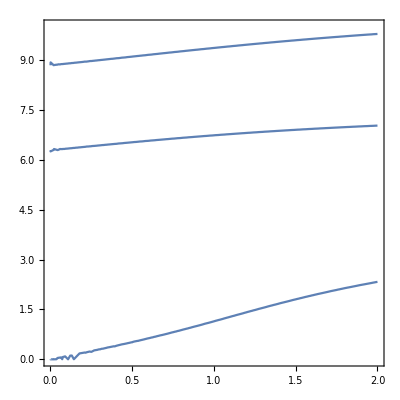

```mathematica
thirdOrder = FullSimplify[Normal[Series[Det[((STM[[1 ;; 3, 1 ;; 6]] /. {t -> (t2 - t1), x-> 1}) .(itm /. { t-> t1 ,x-> 1}))  [[1;;2,1;;2]]], {t1,0,3}]]]

ContourPlot[1/2 t1^2 (16+(-16+3 t1 t2) Cos[t2]-(5 t1+6 t2) Sin[t2]) == 0, {t1, 0.001, 2}, {t2, 0.001, 10}]
```